Local

```mathematica
Needs["DatabaseLink`"];(*databaselink library install*)
connection = OpenSQLConnection["mysql"];(*connecting to database*)
```

```mathematica
data = SQLExecute[connection,"select * from gdelt where DATEADDED='2023-03-18'and IsRootEvent = '1' and (ActionGeo_Type = '2' or ActionGeo_Type = '3')"];(*selecting data with IsRootEvent = '1' from 18th march,2023 , only from USA for local study using parameter ActionGeo_Type = '2'or'3'*)
```

```mathematica
goldstein = ToExpression[data[[All,31]]];(*Goldstein scale of all events*)
avgtone =  ToExpression[data[[All,35]]];(*AvgTone of all events*)
nummentions =  ToExpression[data[[All,32]]];(*NumMentions of all events*)
numsources =  ToExpression[data[[All,33]]];(*NumSources of all events*)
happydata=Select[data,ToExpression[#[[31]]]>=0&];(*Selecting data with only positive goldstein scale*)
saddata=Select[data,ToExpression[#[[31]]]<0&];(*Selecting data with only negative goldstein scale*)
normalize[variable_]:=((variable-Min[variable])/(Max[variable]-Min[variable]))(*Creating function for Min-Max normalization*)
goldsteinhappy= normalize[ToExpression/@happydata[[All,31]]];(*Normalized positive goldstein scale*)
goldsteinsad = normalize[ToExpression/@saddata[[All,31]]];(*Normalized negative goldstein scale*)
avgtonehappy= normalize[ToExpression/@happydata[[All,35]]];(*Normalized avgtone of events with positive goldstein scale*)
mentionshappy= normalize[ToExpression/@happydata[[All,32]]];(*Normalized NumMentions of events with positive goldstein scale*)
sourceshappy= normalize[ToExpression/@happydata[[All,33]]];(*Normalized NumSources of events with positive goldstein scale*)
avgtonesad= normalize[ToExpression/@saddata[[All,35]]];(*Normalized avgtone of events with negative goldstein scale*)
mentionssad= normalize[ToExpression/@saddata[[All,32]]];(*Normalized NumMentions of events with negative goldstein scale*)
sourcessad= normalize[ToExpression/@saddata[[All,33]]];(*Normalized NumSources of events with negative goldstein scale*)
corrimpact = 0.4;(*Approximate rounded weighing factor of average tone based on correlation test*)
```

Goldstein scale and Average tone

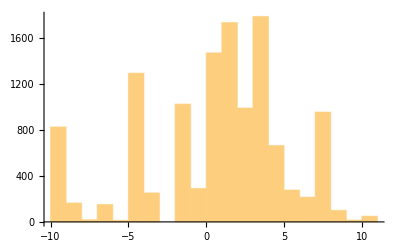

```mathematica
goldsteinscale =Histogram[goldstein](*Histogram of Goldstein scale*)
```

```mathematica
g=DistributionFitTest[goldstein,Automatic,"HypothesisTestData"](*Normal distribution fit of Goldstein scale*)
```

HypothesisTestData[…]

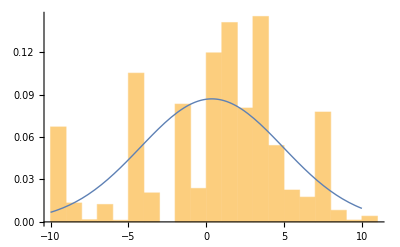

```mathematica
Show[Histogram[goldstein,Automatic,"ProbabilityDensity"],Plot[PDF[g["FittedDistribution"],x],{x,-10,10},PlotStyle->Thick]](*Plot of normal distribution funciton and golstein scale histogram*)
```

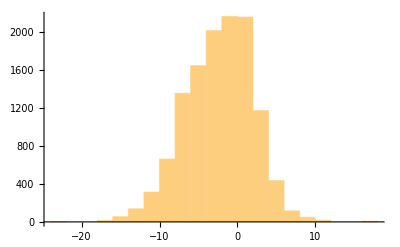

```mathematica
averagetone =Histogram[avgtone](*Histogram of average tone*)
```

```mathematica
t=DistributionFitTest[avgtone,Automatic,"HypothesisTestData"](*Normal distribution fit of avg tone*)
```

HypothesisTestData[…]

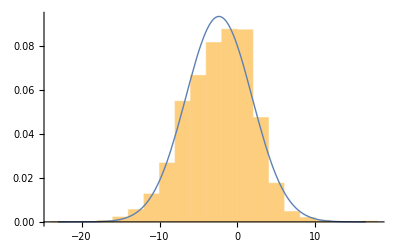

```mathematica
Show[Histogram[avgtone,Automatic,"ProbabilityDensity"],Plot[PDF[t["FittedDistribution"],x],{x,avgtone//Min,avgtone//Max},PlotStyle->Thick]](*Plot of normal distribution function and avgtone histogram*)
```

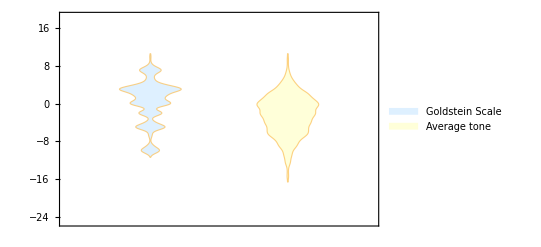

```mathematica
DistributionChart[{goldstein,avgtone},ChartLegends->{"Goldstein Scale","Average tone"},ChartStyle->{LightBlue,LightYellow}](*Distribution chart of Goldstein scale and avgTone*)
```

```mathematica
c=CorrelationTest[Transpose[{goldstein,avgtone}],Automatic,"HypothesisTestData"](*Correlation test of Goldstein scale and avgTone*)
c["TestDataTable"]
c["TestConclusion"]
```

HypothesisTestData[…]

| Statistic | P-Value
Spearman Rank | 0.383404 | 0.

The null hypothesis that the population rank correlation coefficient is equal to 0. is rejected at the 5 percent level based on the Spearman Rank test.

NumMentions and NumSources

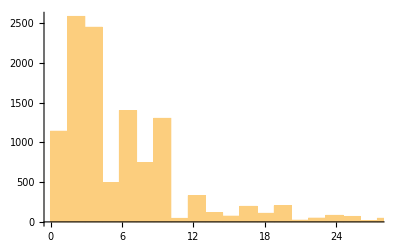

```mathematica
Nummentions=Histogram[nummentions](*Histogram of numeric mentions*)
```

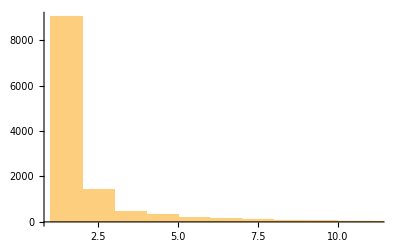

```mathematica
Numsources=Histogram[numsources](*Histogram of numeric sources*)
```

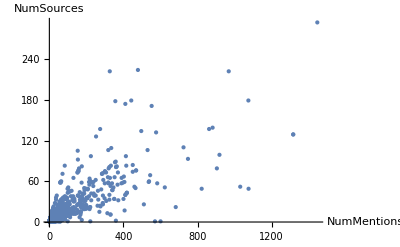

```mathematica
ListPlot[Transpose[{nummentions,numsources}],{AxesLabel->{"NumMentions","NumSources"},PlotRange->All,PlotStyle->PointSize[Small]}](*ListPlot of NumericMentions and NumericSources*)
```

```mathematica
c=CorrelationTest[Transpose[{nummentions,numsources}],Automatic,"HypothesisTestData"](*Correlation test of NumericMentions and NumericSources*)
c["TestDataTable"]
c["TestConclusion"]
```

HypothesisTestData[…]

| Statistic | P-Value
Spearman Rank | 0.598947 | 0.

The null hypothesis that the population rank correlation coefficient is equal to 0. is rejected at the 5 percent level based on the Spearman Rank test.

Correlation Matrix

```mathematica
data1=N[Transpose[{goldsteinhappy,avgtonehappy,mentionshappy,sourceshappy}]];(*making set of all 4 factors of positive goldstien scale*)
data2=N[Transpose[{goldsteinsad,avgtonesad,mentionssad,sourcessad}]];(*making set of all 4 factors of negative goldstien scale*)

correlationMatrix1=Correlation[data1];(*Correlation between all 4 values*)
correlationMatrix2=Correlation[data2];
```

```mathematica
(*Correlation Plot of factors of negative goldstien scale*)
arraysad=ArrayPlot[correlationMatrix2,PlotTheme->"Web",PlotLegends->Automatic,Epilog->{Black,FontSize->14,MapIndexed[Text[Round[#1,0.001],Reverse[#2-0.5]]&,Reverse[correlationMatrix2],{2}]}]
```

-Graphics-

```mathematica
(*Correlation Plot of factors of positive goldstien scale*)
arrayhappy=ArrayPlot[correlationMatrix1,PlotTheme->"Web",PlotLegends->Automatic,Epilog->{Black,FontSize->14,MapIndexed[Text[Round[#1,0.001],Reverse[#2-0.5]]&,Reverse[correlationMatrix1],{2}]}]
```

-Graphics-

Linear relations

```mathematica
data1 = Transpose[{goldstein,avgtone,numsources,nummentions}];
lm1 = LinearModelFit[data1,{GoldsteinScale,Avgtone,NumSources},{GoldsteinScale,Avgtone,NumSources}](*Linear model fit for NumMentions as dependent variable*)
lm1["BestFit"]
lm1["ANOVATable"]
lm1["ParameterTable"]
```

FittedModel[1.28831+0.0924758 Avgtone+0.00726889 GoldsteinScale+4.43431 NumSources]

1.28831+0.0924758 Avgtone+0.00726889 GoldsteinScale+4.43431 NumSources

General::munfl: Exp[-6921.35] is too small to represent as a normalized machine number; precision may be lost.

| DF | SS | MS | F-Statistic | P-Value
GoldsteinScale | 1 | 1349.04 | 1349.04 | 1.57238 | 0.209885
Avgtone | 1 | 26669.5 | 26669.5 | 31.0847 | 2.52205×10^-8
NumSources | 1 | 2.19126×10^7 | 2.19126×10^7 | 25540.4 | 0.
Error | 12324 | 1.05735×10^7 | 857.962 |  | 
Total | 12327 | 3.25142×10^7 |  |  |

General::munfl: Exp[-6921.35] is too small to represent as a normalized machine number; precision may be lost.

| Estimate | Standard Error | t-Statistic | P-Value
1 | 1.28831 | 0.321047 | 4.01285 | 0.0000603451
GoldsteinScale | 0.00726889 | 0.0622353 | 0.116797 | 0.907023
Avgtone | 0.0924758 | 0.0670493 | 1.37922 | 0.167852
NumSources | 4.43431 | 0.0277468 | 159.814 | 0.

```mathematica
data2 = Transpose[{avgtone,nummentions,numsources,goldstein}];(*Linear model fit for Goldstein scale as dependent variable*)
lm2 = LinearModelFit[data1,{Avgtone,NumMentions,NumSources},{Avgtone,NumMentions,NumSources}]
lm2["BestFit"]
lm2["ANOVATable"]
lm2["ParameterTable"]
```

FittedModel[1.28831+0.00726889 Avgtone+0.0924758 NumMentions+4.43431 NumSources]

1.28831+0.00726889 Avgtone+0.0924758 NumMentions+4.43431 NumSources

General::munfl: Exp[-6921.35] is too small to represent as a normalized machine number; precision may be lost.

| DF | SS | MS | F-Statistic | P-Value
Avgtone | 1 | 1349.04 | 1349.04 | 1.57238 | 0.209885
NumMentions | 1 | 26669.5 | 26669.5 | 31.0847 | 2.52205×10^-8
NumSources | 1 | 2.19126×10^7 | 2.19126×10^7 | 25540.4 | 0.
Error | 12324 | 1.05735×10^7 | 857.962 |  | 
Total | 12327 | 3.25142×10^7 |  |  |

General::munfl: Exp[-6921.35] is too small to represent as a normalized machine number; precision may be lost.

| Estimate | Standard Error | t-Statistic | P-Value
1 | 1.28831 | 0.321047 | 4.01285 | 0.0000603451
Avgtone | 0.00726889 | 0.0622353 | 0.116797 | 0.907023
NumMentions | 0.0924758 | 0.0670493 | 1.37922 | 0.167852
NumSources | 4.43431 | 0.0277468 | 159.814 | 0.

```mathematica
data3= Transpose[{goldstein,nummentions,numsources,avgtone}];
lm3 = LinearModelFit[data1,{GoldsteinScale,NumMentions,NumSources},{GoldsteinScale,NumMentions,NumSources}](*Linear model fit for Avgtone as dependent variable*)
lm3["BestFit"]
lm3["ANOVATable"]
lm3["ParameterTable"]
```

FittedModel[1.28831+0.00726889 GoldsteinScale+0.0924758 NumMentions+4.43431 NumSources]

1.28831+0.00726889 GoldsteinScale+0.0924758 NumMentions+4.43431 NumSources

General::munfl: Exp[-6921.35] is too small to represent as a normalized machine number; precision may be lost.

| DF | SS | MS | F-Statistic | P-Value
GoldsteinScale | 1 | 1349.04 | 1349.04 | 1.57238 | 0.209885
NumMentions | 1 | 26669.5 | 26669.5 | 31.0847 | 2.52205×10^-8
NumSources | 1 | 2.19126×10^7 | 2.19126×10^7 | 25540.4 | 0.
Error | 12324 | 1.05735×10^7 | 857.962 |  | 
Total | 12327 | 3.25142×10^7 |  |  |

General::munfl: Exp[-6921.35] is too small to represent as a normalized machine number; precision may be lost.

| Estimate | Standard Error | t-Statistic | P-Value
1 | 1.28831 | 0.321047 | 4.01285 | 0.0000603451
GoldsteinScale | 0.00726889 | 0.0622353 | 0.116797 | 0.907023
NumMentions | 0.0924758 | 0.0670493 | 1.37922 | 0.167852
NumSources | 4.43431 | 0.0277468 | 159.814 | 0.

```mathematica
data4 = Transpose[{goldstein,nummentions,avgtone,numsources}];
lm4 = LinearModelFit[data1,{GoldsteinScale,NumMentions,Avgtone},{GoldsteinScale,NumMentions,Avgtone}](*Linear model fit for NumSources as dependent variable*)
lm4["BestFit"]
lm4["ANOVATable"]
lm4["ParameterTable"]
```

FittedModel[1.28831+4.43431 Avgtone+0.00726889 GoldsteinScale+0.0924758 NumMentions]

1.28831+4.43431 Avgtone+0.00726889 GoldsteinScale+0.0924758 NumMentions

General::munfl: Exp[-6921.35] is too small to represent as a normalized machine number; precision may be lost.

| DF | SS | MS | F-Statistic | P-Value
GoldsteinScale | 1 | 1349.04 | 1349.04 | 1.57238 | 0.209885
NumMentions | 1 | 26669.5 | 26669.5 | 31.0847 | 2.52205×10^-8
Avgtone | 1 | 2.19126×10^7 | 2.19126×10^7 | 25540.4 | 0.
Error | 12324 | 1.05735×10^7 | 857.962 |  | 
Total | 12327 | 3.25142×10^7 |  |  |

General::munfl: Exp[-6921.35] is too small to represent as a normalized machine number; precision may be lost.

| Estimate | Standard Error | t-Statistic | P-Value
1 | 1.28831 | 0.321047 | 4.01285 | 0.0000603451
GoldsteinScale | 0.00726889 | 0.0622353 | 0.116797 | 0.907023
NumMentions | 0.0924758 | 0.0670493 | 1.37922 | 0.167852
Avgtone | 4.43431 | 0.0277468 | 159.814 | 0.

AEI (Anticipated Event Impact)

```mathematica
happiness= (Mean[{goldsteinhappy , corrimpact*avgtonehappy}])+mentionshappy ;(*Calculating AEI value of Positive goldstein scale*)
sadness= (Mean[{goldsteinsad , corrimpact*avgtonesad}])+mentionssad ;(*Calculating AEI value of negative goldstein scale*)
happinessnormalized = normalize[happiness]*10;(*AEI values normalized*)
sadnessnormalized = normalize[sadness]*-10;(*AEI values normalized*)
```

```mathematica
v=Join[Table[Append[happydata[[i,{13,23,58,51}]],happinessnormalized[[i]]],{i,happydata//Length}],Table[Append[saddata[[i,{13,23,58,51}]],sadnessnormalized[[i]]],{i,saddata//Length}]];(*joining AEI data with other parameters like actor type, location, sourceURL*)
```

```mathematica
states=Table[StringReplace[StringSplit[v[[i,4]],","][[-2]]," "->""],{i,Length[v]}];(*String operation to extract location state names*)
```

```mathematica
set= {v[[All,1]],v[[All,2]],v[[All,3]],v[[All,4]],states,v[[All,-1]]}//Transpose;
```

```mathematica
dateofdata = StringJoin[ToString/@data[[1,-2,1]]];
averagesentiment[statename_]:=Select[set,#[[-2]]==statename&][[All,-1]]//Mean(*Calculating average AEI for each state*)
topgroup[statename_,num_]:=If[Length[x=ReverseSortBy[Select[Select[set,#[[-2]]==statename&][[All,{1,2}]]//Flatten,StringLength[#]>0&]//Tally,Last]]<num,x[[1,1]],x[[num,1]]](*calculating top 3 groups responsible for average AEI of a state*)
```

```mathematica
actortype = Import[FileNameJoin[{NotebookDirectory[],"intermediate files","actortyperules.mx"}]];(*Importing actortype rules to convert shortform to fullform*)
distinct=Tally[set[[All,-2]]][[All,1]];(*tally function to get total distinct group types*)
```

```mathematica
s=Table[{dateofdata,distinct[[i]],averagesentiment[distinct[[i]]],topgroup[distinct[[i]],1]//Replace[actortype],topgroup[distinct[[i]],2]//Replace[actortype],topgroup[distinct[[i]],3]//Replace[actortype]},{i,distinct//Length}];(*Creating final table with date, average AEI, state of USA as location and Responsible groups*)
```

```mathematica
s=Prepend[s,{"date","location","average AEI","Group1","Group2","Group3"}];(*Attaching columns names*)
```

```mathematica
s//TableForm(*Final table with all states of USA*)
```

date | location | average AEI | Group1 | Group2 | Group3
2023318 | Alaska | 0.546153 | Government | Civilian | Police forces
2023318 | Iowa | 0.281294 | Media | Government | Education
2023318 | NorthDakota | 0.183706 | Education | Business | Legislature
2023318 | NewYork | -0.0151177 | Judiciary | Government | Media
2023318 | DistrictofColumbia | 0.369121 | Government | Judiciary | Business
2023318 | California | 0.525725 | Education | Civilian | Government
2023318 | NorthCarolina | 0.108362 | Judiciary | Education | Legislature
2023318 | Massachusetts | 0.641283 | Police forces | Education | Civilian
2023318 | Virginia | 0.182837 | Police forces | Government | Judiciary
2023318 | Oklahoma | 1.10117 | Business | Judiciary | Government
2023318 | Michigan | 0.150018 | Education | Police forces | Judiciary
2023318 | Oregon | 1.10244 | Education | Civilian | Government
2023318 | Delaware | 0.578557 | Government | Business | Police forces
2023318 | Connecticut | 1.03868 | Business | Government | Education
2023318 | NewHampshire | 0.786828 | Judiciary | Police forces | Government
2023318 | Ohio | 0.0640209 | Government | Civilian | Police forces
2023318 | Texas | 0.309265 | Police forces | Government | Judiciary
2023318 | Utah | 0.923292 | Government | Civilian | Political opposition
2023318 | NewJersey | -0.069708 | Education | Government | Judiciary
2023318 | Idaho | 0.150824 | Government | Judiciary | Education
2023318 | Arizona | 0.33086 | Government | Police forces | Judiciary
2023318 | Nevada | 0.326686 | Education | Judiciary | Civilian
2023318 | Florida | 0.289037 | Government | Education | Judiciary
2023318 | Maine | 0.982923 | Civilian | Business | Government
2023318 | Washington | 0.525432 | Government | Education | Police forces
2023318 | Minnesota | 0.268151 | Police forces | Education | Government
2023318 | Indiana | 0.919409 | Police forces | Civilian | Government
2023318 | Kentucky | 0.394094 | Legislature | Government | Education
2023318 | Louisiana | 0.658928 | Judiciary | Government | Police forces
2023318 | WestVirginia | 1.01837 | Education | Business | Civilian
2023318 | Colorado | 0.797865 | Education | Government | Judiciary
2023318 | Pennsylvania | 0.300163 | Education | Government | Judiciary
2023318 | Missouri | 0.357916 | Police forces | Judiciary | Civilian
2023318 | Kansas | 0.931576 | Judiciary | Police forces | Education
2023318 | Illinois | 0.41807 | Police forces | Government | Civilian
2023318 | Arkansas | 0.811516 | Education | Judiciary | Government
2023318 | Alabama | 0.560382 | Government | Education | Police forces
2023318 | Tennessee | 0.596184 | Civilian | Education | Business
2023318 | Georgia | 0.374823 | Police forces | Government | Education
2023318 | Wisconsin | 0.756403 | Legislature | Government | Police forces
2023318 | Montana | 0.304904 | Police forces | Education | Legislature
2023318 | Wyoming | 0.339032 | Government | Judiciary | Legislature
2023318 | Vermont | 1.07944 | Government | Judiciary | Education
2023318 | NewMexico | 1.14905 | Government | Legislature | Education
2023318 | SouthDakota | 0.840444 | Government | Business | Judiciary
2023318 | Hawaii | 0.904495 | Business | Government | Military
2023318 | Maryland | 0.720406 | Education | Government | Media
2023318 | Nebraska | 0.612054 | Legislature | Judiciary | Education
2023318 | SouthCarolina | 0.670643 | Judiciary | Government | Media
2023318 | PuertoRico | 0.50012 | Education | Education | Education
2023318 | Mississippi | -0.150269 | Education | Judiciary | Government
2023318 | RhodeIsland | 0.677915 | Media | Civilian | Government

```mathematica
toppositivenews = ReverseSortBy[set[[All,{3,4,6}]],Last][[;;5]]//TableForm(*Top 5 trending positive news of the day based on AEI scale*)
```

https://santamariatimes.com/news/national/govt-and-politics/judge-orders-more-trump-lawyer-testimony-in-mar-a-lago-probe/article_2eadb810-3712-5e2d-ae66-5cc3cdd9836a.html | Washington, District of Columbia, United States | 10.
https://mynorthwest.com/3859859/tejano-musician-fito-olivares-dies-in-houston-at-75/ | Houston, Texas, United States | 7.49794
https://menafn.com/1105805639/Manhattan-Neighborhood-Network-To-Honor-Trailblazer-Ralph-Mcdaniels-During-Celebration-Of-New-Multimedia-Facility | New York, United States | 7.31774
https://ktvz.com/politics/cnn-us-politics/2023/03/17/trump-attorney-ordered-to-testify-before-grand-jury-investigating-former-president/ | Florida, United States | 6.5899
https://vancouversun.com:443/entertainment/celebrity/dark-moments-sam-neill-receives-treatment-for-blood-cancer/wcm/a302ffc5-fc04-4029-b2f6-15a9ec2f1f9c | Hollywood, California, United States | 6.5251

```mathematica
topnegativenews=SortBy[set[[All,{3,4,6}]],Last][[;;5]]//TableForm(*Top 5 trending negative news of the day based on AEI scale*)
```

https://www.durangoherald.com/articles/wyoming-governor-signs-measure-prohibiting-abortion-pills/ | Wyoming, United States | -10.
https://santamariatimes.com/news/national/govt-and-politics/judge-orders-more-trump-lawyer-testimony-in-mar-a-lago-probe/article_2eadb810-3712-5e2d-ae66-5cc3cdd9836a.html | Washington, District of Columbia, United States | -8.76943
https://www.kuaf.com/npr-news/2023-03-18/trump-claims-that-he-will-be-arrested-next-week | Manhattan, New York, United States | -8.04908
https://torontosun.com/news/world/accused-wife-killer-made-prophetic-joke-as-family-feud-contestant | New York, United States | -7.46905
https://theconservativetreehouse.com/blog/2023/03/17/happy-saint-patricks-day/ | Manhattan, New York, United States | -7.21884